```mathematica
Min[Times@@@(((#[[1]]!^#[[2]])#[[2]]!&/@Tally[#])&/@IntegerPartitions[10])]
```

288

```mathematica
Table[Min[Times@@@(((#[[1]]!^#[[2]])#[[2]]!&/@Tally[#])&/@IntegerPartitions[n])],{n,1,40}]
```

{1,2,2,4,8,12,24,48,96,288,576,1152,2304,6912,13824,27648,82944,165888,497664,1327104,2985984,7962624,19906560,59719680,143327232,358318080,955514880,2866544640,7644119040,17199267840,51597803520,137594142720,412782428160,1238347284480,3302259425280,9906778275840,29720334827520,89161004482560,237762678620160,713288035860480}

```mathematica
l=%
```

{1,2,2,4,8,12,24,48,96,288,576,1152,2304,6912,13824,27648,82944,165888,497664,1327104,2985984,7962624,19906560,59719680,143327232,358318080,955514880,2866544640,7644119040,17199267840,51597803520,137594142720,412782428160,1238347284480,3302259425280,9906778275840,29720334827520,89161004482560,237762678620160,713288035860480}

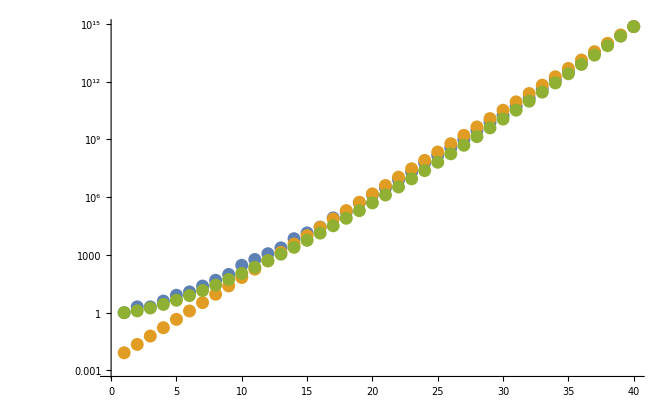

```mathematica
ListLogPlot[{l,Exp[#-5.8]&/@Range[40],(#!)^(.31)&/@Range[40]}]
```

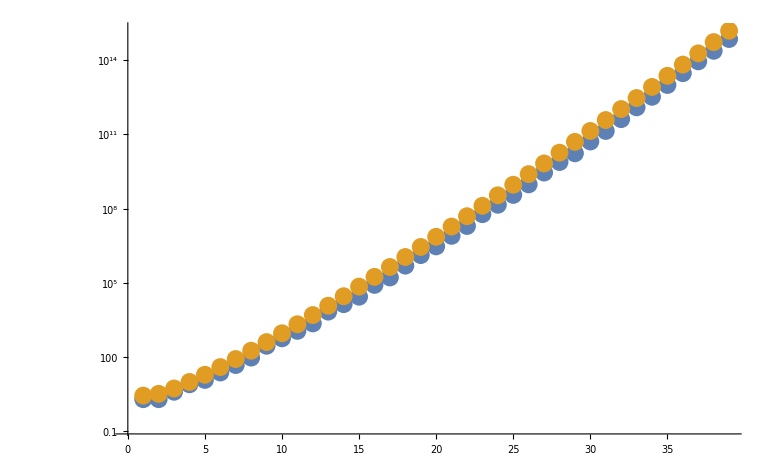

```mathematica
ListLogPlot[{l[[2;;]],(Log[#]!^(#/Log[#])(#/Log[#])!)^.75&/@Range[2,40]}]
```

```mathematica
deg[tp_]:=Times@@(((#[[1]]!)^#[[2]])#[[2]]!&/@tp)
```

```mathematica
Table[MinimalBy[Tally/@IntegerPartitions[n],deg],{n,1,40}];
```

```mathematica
tab=%;
```

```mathematica
tab[[;;,;;,;;,2]]//MatrixForm
```

({{1}}
{{1},{2}}
{{1,1}}
{{1,2}}
{{2,1}}
{{1,1,1}}
{{1,1,2}}
{{1,2,1}}
{{1,2,2}}
{{1,1,1,1},{2,1,2},{1,3,1},{1,2,3}}
{{1,1,1,2},{2,2,1},{1,3,2}}
{{1,1,2,1},{2,2,2}}
{{1,1,2,2}}
{{1,2,1,2},{1,1,3,1},{1,1,2,3},{2,3,2}}
{{1,2,2,1},{1,1,3,2}}
{{1,2,2,2}}
{{1,2,3,1},{1,2,2,3}}
{{1,2,3,2}}
{{1,3,2,2},{1,2,3,3}}
{{2,2,2,2},{1,2,4,2}}
{{1,3,3,2}}
{{2,2,3,2}}
{{1,1,2,3,2}}
{{1,1,3,2,2},{1,1,2,3,3}}
{{2,3,3,2}}
{{1,1,3,3,2}}
{{1,2,2,3,2}}
{{1,2,3,2,2},{1,2,2,3,3},{1,1,3,4,2}}
{{1,2,2,4,2}}
{{1,2,3,3,2}}
{{1,2,3,3,3}}
{{1,2,3,4,2}}
{{1,2,4,3,2},{1,2,3,4,3}}
{{1,3,3,3,2},{1,2,4,3,3}}
{{1,2,4,4,2}}
{{1,3,3,4,2},{1,2,4,4,3}}
{{1,3,4,3,2},{1,3,3,4,3}}
{{1,3,4,3,3}}
{{1,3,4,4,2}}
{{1,3,4,4,3}})

```mathematica
MinimalBy[Tally/@IntegerPartitions[50],deg]
```

{{{6,1},{5,2},{4,3},{3,4},{2,4},{1,2}}}

```mathematica
Timing[t50=Tally/@IntegerPartitions[50];]
```

{1.12217,Null}

```mathematica
Timing[MinimalBy[t50,deg]]
```

{6.91404,{{{6,1},{5,2},{4,3},{3,4},{2,4},{1,2}}}}

```mathematica
Total[{1,2,3,4,5,3,1}*Range[7,1,-1]]
```

72

```mathematica
Timing[MinimalBy[Tally/@IntegerPartitions[72],deg]]
```

{244.56723,{{{6,1},{5,3},{4,5},{3,6},{2,5},{1,3}}}}